tamoaltas - Gráfica de una geodésica en una variedad determinada

-Graphics-

Definiciones

```mathematica
(* Objetos auxiliares *)
n = 2;
```

```mathematica
(* Datos del problema *)
```

```mathematica
(* Coordenadas *)
x[1] = t; x[2] = x; 
dx[1] = dt; dx[2] = dx; (* dx^μ *)
Dx[1] = Dt;Dx[2] = Dx;   (* ∂x^μ *)
```

```mathematica
(* Subscript[C, jk]^i *) 
Do[c[i][j][k]=0,{i,1,n},{j,1,n},{k,1,n}];
c[1][1][2] = 1/x; c[1][2][1] = 1/x; c[2][1][1] = x;
```

```mathematica
(* Y^i, Subscript[α, i], Subscript[T^i, j]*)
vY[1] = t; vY[2] = x;
cα[1]= t; cα[2]= x;
T[1,1] = 0; T[1,2] = (t - x) ; 
T[2,1] = (x - t);T[2,2] = 0;
```

Para Y:

```mathematica
Do [
DYcomp[ν,μ] = D[vY[μ],x[ν]] +  Sum[c[μ][ν][σ] vY[σ], {σ,1,n}],
{ν,1,n},
 {μ,1,n}
];
```

```mathematica
Do[DYp[i,j] = DYcomp[j,i]TensorProduct[Dx[i],dx[j]],{i,1,n},{j,1,n}] ;
DY = Sum[DYp[i,j], {i,1,n},{j,1,n}];
Print[Style["∇Y = ",16],Style[DY,16]]
```

∇Y = 2 Dt⊗dt+(t Dt⊗dx)/x+t x Dx⊗dt+Dx⊗dx

Para α:

```mathematica
Do [
Dαcomp[ν,μ] = D[cα[μ],x[ν]] -  Sum[c[σ][ν][μ] cα[σ], {σ,1,n}],
{ν,1,n},
 {μ,1,n}
];
```

```mathematica
Do[Dαp[i,j] = Dαcomp[j,i]TensorProduct[dx[i],dx[j]],{i,1,n},{j,1,n}] ;
Dα = Sum[Dαp[i,j], {i,1,n},{j,1,n}];
Print[Style["∇α = ",16],Style[ Dα,16]]
```

∇α = (1-x^2) dt⊗dt-(t dt⊗dx)/x-(t dx⊗dt)/x+dx⊗dx

Para T:

```mathematica
Do [
DTcomp[μ,α,β] = (D[T[α,β],x[μ]] +  Sum[c[α][μ][σ] T[σ,β], {σ,1,n}] -  Sum[c[σ][μ][β] T[α,σ], {σ,1,n}] )// Simplify ,
{μ,1,n},
{α,1,n},
{β,1,n}
];
```

```mathematica
Do[DTp[i,j,k] = DTcomp[j,i,k]TensorProduct[Dx[i],dx[k],dx[j]],{i,1,n},{j,1,n},{k,1,n}] ;
DT = Sum[DTp[i,j,k], {i,1,n},{j,1,n}, {k,1,n}];
Print[Style["∇T = ",16],Style[ DT,16]]
```

∇T = -((t-x) (1+x^2) Dt⊗dt⊗dt)/x+Dt⊗dx⊗dt+(-2+t/x) Dt⊗dx⊗dx-Dx⊗dt⊗dt+(t Dx⊗dt⊗dx)/x+((t-x) (1+x^2) Dx⊗dx⊗dt)/x

-Graphics-

```mathematica
vX[1] = t; vX[2] = -x; (* Vector X *)
```

Para Y:

```mathematica
Do [
XDYcomp[μ] = Sum[vX[ν] DYcomp[ν,μ], {ν,1,n}],
{μ,1,n}
];
```

```mathematica
Do[XDYp[i] = XDYcomp[i]Dx[i],{i,1,n}] ;
XDY = Sum[XDYp[i], {i,1,n}];
Print[Style["∇_X Y = ",16],Style[XDY ,16]]
```

∇_X Y = Dt t+Dx (-x+t^2 x)

Para α:

```mathematica
Do [
XDαcomp[μ] = Sum[vX[ν] Dαcomp[ν,μ], {ν,1,n}],
{μ,1,n}
];
```

```mathematica
Do[XDαp[i] = XDαcomp[i]dx[i],{i,1,n}] ;
XDα = Sum[XDαp[i], {i,1,n}];
Print[Style["∇_X α = ",16],Style[XDα   ,16]];
```

∇_X α = dx (-t^2/x-x)+dt (t+t (1-x^2))

Para T:

```mathematica
Do [
XDTcomp[α, β] = Sum[vX[ν] DTcomp[ν, α, β], {ν,1,n}],
{α,1,n},
{β,1,n}
];
```

```mathematica
Do[XDTp[i,j] = XDTcomp[i,j]TensorProduct[Dx[i],dx[j]],{i,1,n},{j,1,n}] ;
XDT = Sum[XDTp[i, j], {i,1,n},{j,1,n}];
Print[Style["∇_X T = ",16],Style[ XDT,16]]
```

∇_X T = -(t (t-x) (1+x^2) Dt⊗dt)/x+(t-(-2+t/x) x) Dt⊗dx-2 t Dx⊗dt+(t (t-x) (1+x^2) Dx⊗dx)/x

-Graphics-

```mathematica
p = {1,1}
```

{1,1}

Para Y:

```mathematica
With[{t=p[[1]], x=p[[2]]}, Evaluate[DY]] (* ∇Y *)
```

2 Dt⊗dt+Dt⊗dx+Dx⊗dt+Dx⊗dx

```mathematica
With[{t=p[[1]], x=p[[2]]}, Evaluate[XDY]] (* ∇_X Y *)
```

Dt

Para α:

```mathematica
With[{t=p[[1]], x=p[[2]]}, Evaluate[Dα]] (* ∇α *)
```

-dt⊗dx-dx⊗dt+dx⊗dx

```mathematica
With[{t=p[[1]], x=p[[2]]}, Evaluate[XDα]] (* ∇_X α *)
```

dt-2 dx

Para T:

```mathematica
With[{t=p[[1]], x=p[[2]]}, Evaluate[DT]] (* ∇T *)
```

Dt⊗dx⊗dt-Dt⊗dx⊗dx-Dx⊗dt⊗dt+Dx⊗dt⊗dx

```mathematica
With[{t=p[[1]], x=p[[2]]}, Evaluate[XDT]] (* ∇_X T *)
```

2 Dt⊗dx-2 Dx⊗dt

-Graphics-
-Graphics-ec. de la geodésica

Para Y:

```mathematica
Clear[σ];
```

```mathematica
Do [
YDYcomp[μ] = Sum[vY[ν] DYcomp[ν,μ], {ν,1,n}];
Print[YDYcomp[μ]],
{μ,1,n}
]
```

3 t

x+t^2 x

No es 0 para ambos componentes, por lo que no se cumple la ec. de la geodésica.

Para X:

```mathematica
Do [
DXcomp[ν,μ] = D[vX[μ],x[ν]] +  Sum[c[μ][ν][σ] vX[σ], {σ,1,n}],
{ν,1,n},
 {μ,1,n}
];
```

```mathematica
Do [
XDXcomp[μ] = Sum[vX[ν] DXcomp[ν,μ], {ν,1,n}];
Print[XDXcomp[μ]],
{μ,1,n}
]
```

-t

x+t^2 x

No es 0 para ambos componentes, por lo que no se cumple la ec. de la geodésica.

-Graphics-

-Graphics-

```mathematica
(* Subscript[C, jk]^i, pero ahora dependiente de λ*) 
Do[c[i][j][k]=0,{i,1,n},{j,1,n},{k,1,n}];
c[1][1][2] = 1/x[λ]; c[1][2][1] = 1/x[λ]; c[2][1][1] = x[λ];
```

```mathematica
(* Condiciones Iniciales *)
iniciales = {t[0]==1,x[0]==1,t'[0]==1,x'[0]==1};
```

```mathematica
γ[1] = t[λ]; γ[2] = x[λ];  (* Geodésica a resolver *)
expresiones = {D[γ[1],{λ, 2}] + Sum[c[1][α][β] D[γ[α],λ] D[γ[β],λ], {α, 1, n}, {β, 1, n} ] == 0,
D[γ[2],{λ, 2}] + Sum[c[2][α][β] D[γ[α],λ] D[γ[β],λ], {α, 1, n}, {β, 1, n} ] == 0}
```

{(2 t'[λ] x'[λ])/x[λ]+t''[λ]==0,x[λ] t'[λ]^2+x''[λ]==0}

```mathematica
(* Ecuaciones *)
ecs = Join[expresiones, iniciales];
sol = NDSolve[ecs,{t[λ],x[λ]},{λ,0, 10}]
```

{{t[λ]→InterpolatingFunction[…][λ],x[λ]→InterpolatingFunction[…][λ]}}

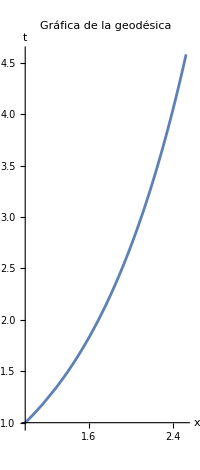

```mathematica
curva = ParametricPlot[{t[λ],x[λ]}/. sol, {λ,0, 10} ,AxesLabel->{x,t}];
Show[curva,PlotLabel->"Gráfica de la geodésica"]
```